## The Hamiltonian

```mathematica
SetDirectory[NotebookDirectory[]];
```

### Basic definitions

```mathematica
ndim=2;
nbody=2;
If[ndim==2,
position={{qax,qay},{qbx,qby}};
p={{pax,pay},{pbx,pby}};
m={ma,mb};
xdot={{qaxdot1,qaydot1},{qbxdot1,qbydot1}};
pdot={{paxdot1,paydot1},{pbxdot1,pbydot1}};
,
position={{qax,qay,qaz},{qbx,qby,qbz}};
p={{pax,pay,paz},{pbx,pby,pbz}};
m={ma,mb};
xdot={{qaxdot1,qaydot1,qazdot1},{qbxdot1,qbydot1,qbzdot1}};
pdot={{paxdot1,paydot1,pazdot1},{pbxdot1,pbydot1,pbzdot1}};
]
If[nbody==3,
If[ndim==3,
AppendTo[position,{qcx,qcy,qcz}];
AppendTo[p,{pcx,pcy,pcz}];
AppendTo[m,mc];
AppendTo[xdot,{qcxdot1,qcydot1,qczdot1}];
AppendTo[pdot,{pcxdot1,pcydot1,pczdot1}];
,
AppendTo[position,{qcx,qcy}];
AppendTo[p,{pcx,pcy}];
AppendTo[m,mc];
AppendTo[xdot,{qcxdot1,qcydot1}];
AppendTo[pdot,{pcxdot1,pcydot1}];
]
]
```

### Functions

```mathematica
Normv[x_List] := Sqrt[x.x]
Normvector[x_List] := x/Normv[x]
rab[a_Integer,b_Integer] := position[[a]] - position[[b]]
Normvsq[x_List] := x.x
nhat[a_Integer,b_Integer] := Normvector[rab[a,b]]
nhatx[a_Integer,b_Integer,i_Integer] := nhat[a,b][[i]]
rdot[a_Integer,b_Integer] := xdot[[a]] - xdot[[b]]
R[a_Integer,b_Integer] :=Normv[rab[a,b]]
psq[a_Integer] := p[[a]].p[[a]]
mline[a_Integer]:=√(m[[a]]^2+psq[a])
y[a_Integer,b_Integer]:=mline[a]^-1 √(m[[a]]^2+(nhat[a,b].p[[a]])^2)
```

### Units

```mathematica
(*G=1;
CC=1;*)
```

### The Hamiltonian

```mathematica
W=ConstantArray[0,4];
```

```mathematica
W[[1]]=Sum[mline[a],{a,1,nbody}];
```

```mathematica
W[[2]]=-1/2 G Sum[If[b==a,0,(mline[a]mline[b])/R[a,b](1+psq[a]/mline[a]^2+psq[b]/mline[b]^2)],{a,1,nbody},{b,1,nbody}];
```

```mathematica
W[[3]]=1/4 G Sum[If[b==a,0,1/R[a,b](7p[[a]].p[[b]]+(p[[a]].nhat[a,b])(p[[b]].nhat[a,b]))],{a,1,nbody},{b,1,nbody}];
```

```mathematica
W[[4]]=-1/4 G Sum[If[b==a,0,1/R[a,b](mline[a]mline[b])^-1/((y[b,a]+1)^2 y[b,a])(2(2(p[[a]].p[[b]])^2(p[[b]].nhat[b,a])^2-2(p[[a]].nhat[b,a])(p[[b]].nhat[b,a])(p[[a]].p[[b]])psq[b]+(p[[a]].nhat[b,a])^2 psq[b]^2-(p[[a]].p[[b]])^2 psq[b])1/mline[b]^2+2(-psq[a](p[[b]].nhat[b,a])^2+(p[[a]].nhat[b,a])^2(p[[b]].nhat[b,a])^2+2(p[[a]].nhat[b,a])(p[[b]].nhat[b,a])(p[[a]].p[[b]])+(p[[a]].p[[b]])^2-(p[[a]].nhat[b,a])^2 psq[b])+(-3psq[a](p[[b]].nhat[b,a])^2+(p[[a]].nhat[b,a])^2(p[[b]].nhat[b,a])^2+8(p[[a]].nhat[b,a])(p[[b]].nhat[b,a])(p[[a]].p[[b]])+psq[a]psq[b]-3(p[[a]].nhat[b,a])^2 psq[b])y[b,a])],{a,1,nbody},{b,1,nbody}];
```

### Post-Minkowski Approximation

```mathematica
<<Format1.m
<<Optimize.m
```

```mathematica
PM1=Sum[W[[a]],{a,1,4}];
```

#### 2D

```mathematica
pdot0=Table[D[-PM1,position[[ibody]][[idim]]],{ibody,1,nbody},{idim,1,ndim}];
qdot0 =Table[D[PM1,p[[ibody]][[idim]] ],{ibody,1,nbody},{idim,1,ndim}];
```

```mathematica
pdot0c = CAssign[pdot0,pdot0,"OptimizationSymbol"->z];
qdot0c = CAssign[qdot0,qdot0,"OptimizationSymbol"->o];
```

```mathematica
equations={qdot0,pdot0,PM1};
eq=CAssign[equations,equations,"OptimizationSymbol"->o];
```

```mathematica
Export["equations.txt",eq]
Export["pdot0.txt",pdot0c]
Export["qdot0.txt",qdot0c]
```

equations.txt

pdot0.txt

qdot0.txt

```mathematica
(*eq0=ConstantArray[0,8];
eq0[[1]]=D[PM1,pax];
eq0[[2]]=D[PM1,pay];
eq0[[3]]=-D[PM1,qax];
eq0[[4]]=-D[PM1,qay];
eq0[[5]]=D[PM1,pbx];
eq0[[6]]=D[PM1,pby];
eq0[[7]]=-D[PM1,qbx];
eq0[[8]]=-D[PM1,qby];

Export["dqax.txt",CForm[eq0[[1]]]];
Export["dqay.txt",CForm[eq0[[2]]]];
Export["dpax.txt",CForm[eq0[[3]]]];
Export["dpay.txt",CForm[eq0[[4]]]];
Export["dqbx.txt",CForm[eq0[[5]]]];
Export["dqby.txt",CForm[eq0[[6]]]];
Export["dpbx.txt",CForm[eq0[[7]]]];
Export["dpby.txt",CForm[eq0[[8]]]];*)
```

#### 3D

```mathematica
(*eq0=ConstantArray[0,12];
eq0[[1]]=D[PM1,pax];
eq0[[2]]=D[PM1,pay];
eq0[[3]]=D[PM1,paz];
eq0[[4]]=-D[PM1,qax];
eq0[[5]]=-D[PM1,qay];
eq0[[6]]=-D[PM1,qaz];
eq0[[7]]=D[PM1,pbx];
eq0[[8]]=D[PM1,pby];
eq0[[9]]=D[PM1,pbz];
eq0[[10]]=-D[PM1,qbx];
eq0[[11]]=-D[PM1,qby];
eq0[[12]]=-D[PM1,qbz];*)
```

### Calculating Conservation of Angular Momentum

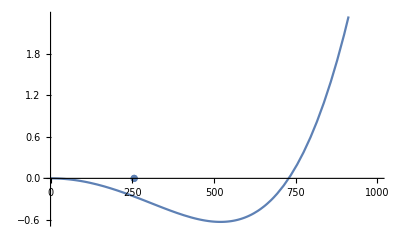

o5=r*r
        o4=m1*m1
        o3=pθ*pθ
        o14=m2*m2
        o6=o4*o5
        o7=o3+o6
        o23=r**(-2)
        o24=o23*o3
        (init(pθ)*r**8)/pθ**2=(G*(1.d1*o5*pθ**6+1.4000000000000001d1*o4*
     &  pθ**4*r**4-o14*o3*o4*r**6-3.d0*m1**4*o14*r**8))/o7**2+r**7*(-(sq
     &  rt(o14+o24)/(o3+o14*o5))-sqrt(o24+o4)/o7)

```mathematica
E1=√(pcan^2+m1^2);E2=√(pcan^2+m2^2);mtot=m1+m2;v=(m1 m2)/mtot^2;Etot=E1+E2;ξ=(E1 E1)/Etot^2;γ=Etot/mtot;σ=(p1 p2)/(m1 m2);
cpol={(v^2 mtot^2)/(γ^2 ξ)(1-2 σ^2)};
V[pcan_,r_]=cpol[[1]] (pcan^2)G/r/.{p1->-pcan, p2->pcan};
H[pcan_,r_]=√(pcan^2+m1^2)+√(pcan^2+m2^2)+V[pcan,r];
Hpol=H[√(pr^2+pθ^2/r^2),r];
prdot=D[Hpol,r];
init[pθ_]:=Simplify[prdot/.pr->0]
init[pθ];
userG=1;userm1=10;userm2=12;userr=100;
newtonianZero={{√((G (m1 m2)^2 r)/(m1+m2)),0}}/.{r->userr,m1->userm1,m2->userm2,G->userG};
newtonPoint=ListPlot[newtonianZero];
initPlot=Plot[init[pθ]/.{r->userr,m1->userm1,m2->userm2,G->userG},{pθ,0,10userr}];
Show[initPlot,newtonPoint]
```

```mathematica
init0=(init[x] r^8)/x^2/.pθ->x;
init0prime=D[init0,x];
init0prime2=D[init0prime,x];
initexp={init0,init0prime,init0prime2};
initc=CAssign[initexp,initexp,"OptimizationSymbol"->o]
Export["init0.txt",initc]
```

o3=m1*m1;
o10=m2*m2;
o6=x*x;
o4=r*r;
o5=o3*o4;
o7=o5+o6;
o24=pow(r,-2.);
o25=o24*o6;
o8=pow(o7,-2.);
o13=pow(r,6.);
o15=pow(r,4.);
o9=pow(m1,4.);
o11=pow(r,8.);
o12=-3.*o10*o11*o9;
o14=-(o10*o13*o3*o6);
o16=pow(x,4.);
o17=14.*o15*o16*o3;
o18=pow(x,6.);
o19=10.*o18*o4;
o20=o12+o14+o17+o19;
o22=pow(r,7.);
o23=1/o7;
o26=o25+o3;
o27=sqrt(o26);
o29=o10*o4;
o30=o29+o6;
o31=1/o30;
o32=o10+o25;
o33=sqrt(o32);
o45=pow(o7,-3.);
o38=-2.*o10*o13*o3*x;
o39=pow(x,3.);
o40=56.*o15*o3*o39;
o41=pow(x,5.);
o42=60.*o4*o41;
o43=o38+o40+o42;
o47=1./sqrt(o26);
o66=pow(r,-4.);
o52=pow(o30,-2.);
o50=1./sqrt(o32);
initexp[0]=o22*(-(o23*o27)-o31*o33)+G*o20*o8;
initexp[1]=G*o43*o8-4.*G*o20*o45*x+o22*(-(o23*o24*o47*x)-o24*o31*o50*x+2.*o33*o52*x+2.*o27*\
o8*x);
initexp[2]=-4.*G*o20*o45+G*(-2.*o10*o13*o3+300.*o16*o4+168.*o15*o3*o6)*o8-8.*G*o43*o45*x+o2\
2*(-(o23*o24*o47)-o24*o31*o50+2.*o33*o52-8.*o27*o45*o6+4.*o24*o50*o52*o6+2.*o27*o8+4.*o24*\
o47*o6*o8+o23*o6*o66*pow(o26,-1.5)-8.*o33*o6*pow(o30,-3.)+o31*o6*o66*pow(o32,-1.5))+24.*G*\
o20*o6*pow(o7,-4.);

init0.txt